```mathematica
(*This notebook is used to generate figure 4 in the article
"The failure of propagation in heterogeneous reaction-diffusion systems through the method of upper and lower solutions" by 
Courdurier M. and Paduro E.*)
SetDirectory[NotebookDirectory[]];
τ=500;α=0.3;γ=5;xmin=-50;xmax=50;maxtime=400; L=1;
Needs["NDSolve`FEM`"]
```

NDSolveValue::ndsz: At x == 9.51798, step size is effectively zero; singularity or stiff system suspected.

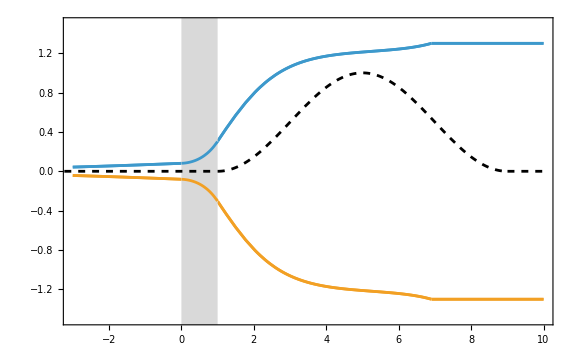

Fig4a.png

```mathematica
(*Experiment 2: testing for a barrier. Double Diffusive. Case (i): Depressed Dynamics, distributed over an interval*)
γ=4.97;pos=5;width=4;vinf=0.01;
Clear[sg1,sg2,sg3,p,K,p1,h,f,v,g,g2,a,δ,V1,W1]
filename= "Fig4a.png";
sg1=1;sg2=1;sg3=1;p=3.7;K=1.3;
p1=p;

f[v_]=v(1-v)(v-α);
h[v_]=Min[f[-v],-f[v]];
If[h[K]-K/γ<0,Print["You must choose a larger K"]]

(*Must satisfy vg(v)<0 for v small*)
g[v_]=-v;
g2[v_]=Min[-g[v],g[-v]];

eqn=FindRoot[h[v]-v/γ==0,{v,0.2}];
eqn2=FindRoot[h[v]-v/γ==0,{v,1.3}];
a1=v/.eqn;
b=v/.eqn2;

(*Step 1: the approach. The interval [a00,a01] is where the hetogeneity will act*)
a=Min[1,a1];
δ=0.2Min[1,a1];
vinf=0.1a;(*0.2a;*)

(*Step 3: The Summit*)
V1=NDSolveValue[{sg1 v''[x]==Which[v[x]>vinf+10^(-5),h[v[x]]-v[x]/γ,True,0],v[0]==a, v'[0]==Sqrt[2]Sqrt[(1/sg1)Integrate[h[u]-u/γ,{u,vinf,a}]]},v,{x,-10,0}];
Plot[V1[x],{x,-10,0}];

V2=NDSolveValue[{sg2 v''[x]==h[v[x]]-v[x]/γ+p1 g2[v[x]],v[0]==V1[0],v'[0]==V1'[0]},v,{x,0,L}];
Plot[V2[x],{x,0,L}];

V3=NDSolveValue[{sg3 v''[x]==h[v[x]]-v[x]/γ,v[L]==V2[L],v'[L]==V2'[L]},v,{x,L,L+10}];
Plot[V3[x],{x,L,L+1}];

(*Together*)
eqnx0=FindRoot[V3[x]==K,{x,L+0.5}];
x0=x/.eqnx0;


VV[x_]=Which[x<0,V1[x],x<L,V2[x],x<x0,V3[x],True,K];

h2[v_,x_]=Which[x<=0,h[v]-v/γ,x<L,h[v]-v/γ+p1 g2[v],True,h[v]-v/γ];

(*g1=Plot[{VV[x],h2[VV[x],x]},{x,-3,5},*)
barrier=Plot[{VV[x],-VV[x]},{x,-3,10},
Frame->True,
PlotRange->{-1.5,1.5},
PlotLegends->Placed[LineLegend[{"",""},LegendMarkerSize->23],{Left,Top}],
FrameTicksStyle->Directive[FontSize->20],
ImageSize->Large
];
barrierAux=Plot[{VV[x],-VV[x]},{x,-3,10}];
rectangleHeterogeneity=Graphics[{LightGray,Rectangle[{0,-2},{L,2}]}];

(*Initial Data*)
pos=5;width=4;
v0[x_]=Piecewise[{{0,x<pos-width},{0.5(1+Cos[Pi(x-pos)/width]),pos-width<=x<=pos+width},{0,x>pos+width}}];
initialData=Plot[v0[x],{x,-4,10},PlotStyle->{Black,Dashed},PlotLegends->Placed[LineLegend[{""},LegendMarkerSize->25],{Left,Top}]];

img=Show[barrier,rectangleHeterogeneity,barrierAux,initialData]
Export[filename,img]
```

```mathematica
(*Case 1: Additive heterogenerity*)
(*Double diffusive case*)
filenamePrefix="Fig4";
pos=5;width=4;
Monitor[
Do[
Switch[case,
1,suffix="b.png";p=0.11;dd2=1;,
2,suffix="c.png";p=0.12;dd2=1;,
3,suffix="d.png";p=3.7;dd2=1;
];
g[v_,x_]=-v *Boole[x>0] *Boole[x<L];
mesh=ToElementMesh[Line[{{xmin},{xmax}}],MaxCellMeasure->0.1];
{V1,W1}=NDSolveValue[{D[u[t, x], t] == Laplacian[u[t,x],{x}] + u[t, x](1-u[t,x])(u[t,x]-α)- w[t,x]+p g[u[t,x],x]+NeumannValue[0,x==xmin||x==xmax], 
τ D[w[t, x], t] == dd2  Laplacian[w[t,x],{x}] + u[t, x] - γ w[t, x]+NeumannValue[0,x==xmin||x==xmax], 
u[0,x]==0.5 (1+Cos[Pi (x-pos)/width])*Boole[Abs[x-pos]<=width], 
w[0, x] ==0},
 {u, w},
 {t, 0, maxtime}, 
Element[x,mesh],
Method->{"MethodOfLines","SpatialDiscretization"->{"FiniteElement"}}
];

g2=ListLinePlot3D[Table[Table[{t,x,V1[t,x]}, {x, xmin, xmax,0.2}],{t,0,maxtime,25}],
PlotRange->{-0.5,1.5},
ScalingFunctions->{"Reverse",None,None},
(*AxesLabel->{"time","x axis","v axis"},*)
ViewPoint->{5,2,3.5},
Ticks->{Table[k,{k,0,400,100}],{-25,0,25,50},{0,0.5,1}},
ImagePadding->20
];
Export[filenamePrefix<>suffix,g2]
,{case,{1,2,3}}]
,"Current: "<>filenamePrefix<>suffix]
```